# Calculating the rotational frequencies ω for ^163Lu

## Using Double-Energy-Shift fitting approach

## The theoretical data-set is transformed in a similar manner as the experimental one

```mathematica
ClearAll["Global`*"]
```

### Experimental data

```mathematica
spins1=Table[i,{i,6.5,48.5,2}];
spins2=Table[i,{i,13.5,45.5,2}];
spins3=Table[i,{i,16.5,42.5,2}];
spins4=Table[i,{i,23.5,41.5,2}];
E0=0;
expEn1={{6.5,0},{8.5,0.1966},{10.5,0.4597},{12.5,0.7746},{14.5,1.1609},{16.5,1.6112},{18.5,2.1265},{20.5,2.7051},{22.5,3.3441},{24.5,4.0411},{26.5,4.7937},{28.5,5.5992},{30.5,6.457},{32.5,7.3667},{34.5,8.3293},{36.5,9.3458},{38.5,10.4169},{40.5,11.5431},{42.5,12.7224},{44.5,13.9491},{46.5,15.2181},{48.5,16.5221}};
TSD1Exp=Map[Function[x,{x[[1]],x[[2]]+E0}],expEn1];
expEn2={{13.5,1.3394},{15.5,1.7467},{17.5,2.2184},{19.5,2.7527},{21.5,3.3484},{23.5,4.003},{25.5,4.7143},{27.5,5.4805},{29.5,6.3004},{31.5,7.1733},{33.5,8.0998},{35.5,9.08},{37.5,10.1147},{39.5,11.2036},{41.5,12.3466},{43.5,13.5441},{45.5,14.7911}};
TSD2Exp=Map[Function[x,{x[[1]],x[[2]]+E0}],expEn2];
expEn3={{16.5,2.1237},{18.5,2.6293},{20.5,3.1973},{22.5,3.8243},{24.5,4.5094},{26.5,5.2506},{28.5,6.0465},{30.5,6.8963},{32.5,7.7988},{34.5,8.7546},{36.5,9.7638},{38.5,10.8268},{40.5,11.9392},{42.5,13.0861}};
TSD3Exp=Map[Function[x,{x[[1]],x[[2]]+E0}],expEn3];
expEn4={{23.5,4.58},{25.5,5.2251},{27.5,5.9273},{29.5,6.6819},{31.5,7.4919},{33.5,8.3573},{35.5,9.2778},{37.5,10.2535},{39.5,11.2851},{41.5,12.3701}};
TSD4Exp=Map[Function[x,{x[[1]],x[[2]]+E0}],expEn4];
```

### Analytic formulas for the excitation energies

```mathematica
(*Fit parameters:numerical values from CXX (imported)*)
a1=1/(2*72);a2=1/(2*15);a3=1/(2*7);v=2.1;gm=22;shiftTSD2=0.3;shiftTSD4=0.6;
(*Analytic formulas for the excitation energies*)
IF[I_]:=1/(2I);
B1[I_,j_,A1_,A2_,A3_,V_,γ_]:=-(((2I-1)(A3-A1)+2j*A1)*((2I-1)(A2-A1)+2j*A1)+8A2*A3*I*j+((2j-1)(A3-A1)+2I*A1+V(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))*((2j-1)(A2-A1)+2I*A1+V(2j-1)/(j(j+1))2 √3 Sin[γ*π/180]));
C1[I_,j_,A1_,A2_,A3_,V_,γ_]:=(((2I-1)(A3-A1)+2j*A1)*((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))√3(√3 Cos[γ*π/180]+Sin[γ*π/180]))-4I*j*A3^2)*(((2I-1)(A2-A1)+2j*A1)*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2 √3 Sin[γ*π/180])-4I*j*A2^2);
HMin[I_,j_,A1_,A2_,A3_,V_,γ_]:=(A2+A3)/2(I+j)+A1(I-j)^2-V*(2j-1)/(j+1)Sin[γ*π/180+π/6];
Omega1[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B1[I,j,A1,A2,A3,V,γ]-(B1[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
Omega2[I_,j_,A1_,A2_,A3_,V_,γ_]:=√(1/2(-B1[I,j,A1,A2,A3,V,γ]+(B1[I,j,A1,A2,A3,V,γ]^2-4C1[I,j,A1,A2,A3,V,γ])^(1/2)));
EWobb[n1_,n2_,I_,j_,A1_,A2_,A3_,V_,γ_]:=HMin[I,j,A1,A2,A3,V,γ]+Omega1[I,j,A1,A2,A3,V,γ](n1+1/2)+Omega2[I,j,A1,A2,A3,V,γ](n2+1/2);
TSD1[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[0,0,I,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD2[I_,A1_,A2_,A3_,V_,γ_,shift_]:=(EWobb[0,0,I,6.5,A1,A2,A3,V,γ]+shift)-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD3[I_,A1_,A2_,A3_,V_,γ_]:=EWobb[1,0,I-1,6.5,A1,A2,A3,V,γ]-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ];
TSD4[I_,A1_,A2_,A3_,V_,γ_,shift_]:=(EWobb[0,0,I,6.5,A1,A2,A3,V,γ]+shift)-EWobb[0,0,6.5,6.5,A1,A2,A3,V,γ]; 
band1[I_]:=TSD1[I,a1,a2,a3,v,gm]+E0;
band2[I_]:=TSD2[I,a1,a2,a3,v,gm,shiftTSD2]+E0;
band3[I_]:=TSD3[I,a1,a2,a3,v,gm]+E0;
band4[I_]:=TSD4[I,a1,a2,a3,v,gm,shiftTSD4]+E0;
TSD1Th=Table[{spins1[[i]],band1[spins1[[i]]]},{i,1,Length[spins1]}];
TSD2Th=Table[{spins2[[i]],band2[spins2[[i]]]},{i,1,Length[spins2]}];
TSD3Th=Table[{spins3[[i]],band3[spins3[[i]]]},{i,1,Length[spins3]}];
TSD4Th=Table[{spins4[[i]],band4[spins4[[i]]]},{i,1,Length[spins4]}];
```

## TSD4: Exp vs Th comparison

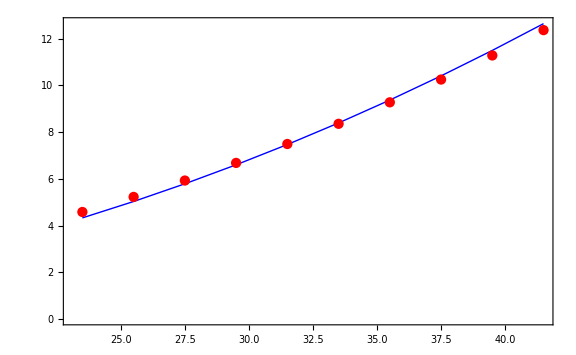

```mathematica
ListPlot[{TSD4Exp,TSD4Th},PlotRange->All,Joined->{False, True},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->Full]
```

## TSD4: δ_(exp-th)

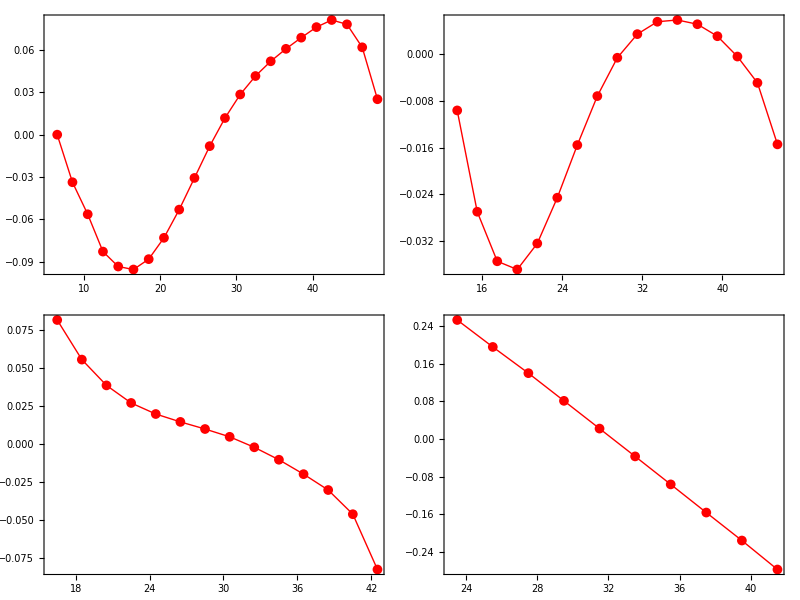

```mathematica
Grid[{{ListPlot[Table[{TSD1Exp[[i,1]],(TSD1Exp[[i,2]]-TSD1Th[[i,2]])},{i,1,Length[TSD1Exp]}],PlotRange->All,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{Red,Thick}],ListPlot[Table[{TSD2Exp[[i,1]],(TSD2Exp[[i,2]]-TSD2Th[[i,2]])},{i,1,Length[TSD2Exp]}],PlotRange->All,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{Red,Thick}]},{ListPlot[Table[{TSD3Exp[[i,1]],(TSD3Exp[[i,2]]-TSD3Th[[i,2]])},{i,1,Length[TSD3Exp]}],PlotRange->All,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{Red,Thick}],ListPlot[Table[{TSD4Exp[[i,1]],(TSD4Exp[[i,2]]-TSD4Th[[i,2]])},{i,1,Length[TSD4Exp]}],PlotRange->All,Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{Red,Thick}]}}]
```

```mathematica
(*Do[Print[StringTemplate["``"][TSD4Exp[[i,1]]]," ",TSD4Th[[i,2]]-TSD4Exp[[i,2]]],{i,1,Length[TSD4Exp]}]*)
Table[
```

## TSD4: adjacent levels difference

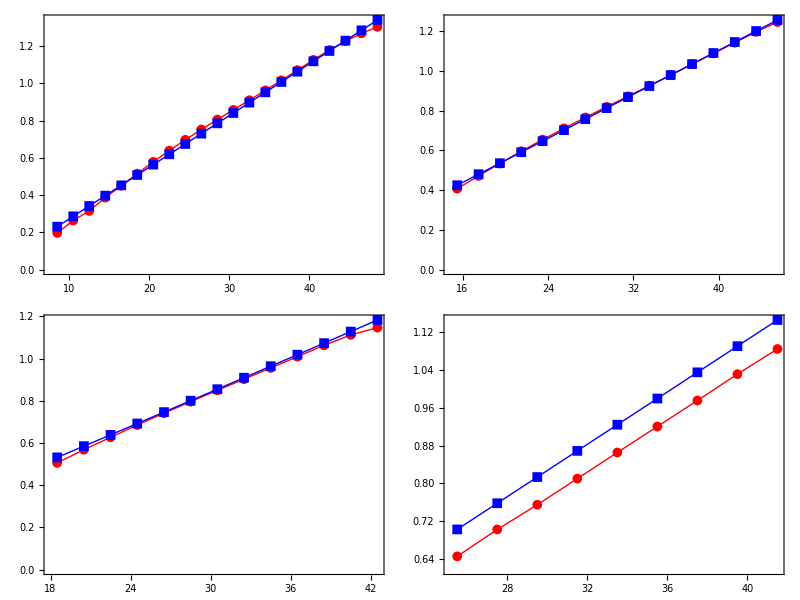

```mathematica
Grid[{{ListPlot[{Table[{TSD1Exp[[i,1]],Abs[(TSD1Exp[[i,2]]-TSD1Exp[[i-1,2]])]},{i,2,Length[TSD1Exp]}],Table[{TSD1Th[[i,1]],Abs[(TSD1Th[[i,2]]-TSD1Th[[i-1,2]])]},{i,2,Length[TSD1Th]}]},PlotRange->All,Joined->{True, True},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->Full],ListPlot[{Table[{TSD2Exp[[i,1]],Abs[(TSD2Exp[[i,2]]-TSD2Exp[[i-1,2]])]},{i,2,Length[TSD2Exp]}],Table[{TSD2Th[[i,1]],Abs[(TSD2Th[[i,2]]-TSD2Th[[i-1,2]])]},{i,2,Length[TSD2Th]}]},PlotRange->All,Joined->{True, True},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->Full]},{ListPlot[{Table[{TSD3Exp[[i,1]],Abs[(TSD3Exp[[i,2]]-TSD3Exp[[i-1,2]])]},{i,2,Length[TSD3Exp]}],Table[{TSD3Th[[i,1]],Abs[(TSD3Th[[i,2]]-TSD3Th[[i-1,2]])]},{i,2,Length[TSD3Th]}]},PlotRange->All,Joined->{True, True},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->Full],ListPlot[{Table[{TSD4Exp[[i,1]],Abs[(TSD4Exp[[i,2]]-TSD4Exp[[i-1,2]])]},{i,2,Length[TSD4Exp]}],Table[{TSD4Th[[i,1]],Abs[(TSD4Th[[i,2]]-TSD4Th[[i-1,2]])]},{i,2,Length[TSD4Th]}]},PlotRange->All,Joined->{True, True},PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,ImageSize->Large,PlotStyle->{{Red,Thick},{Blue,Thick}},PlotRange->Full]}}]
```

## The rotational frequency (exp and theory)

```mathematica
hrot[band_]:=Table[{band[[i,1]],(band[[i,2]]-band[[i-1,2]])/2},{i,2,Length[band]}];
```

### Create exporter function

```mathematica
prepath[path_]:=StringTemplate["/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/163Lu-New-TSD4-Formalism/Resources/Output_Graphs/Double_Shift_Formalism/Rotational_Quantities/``.pdf"][path];
exporter[object_,path_]:=Export[path,object,ImageResolution->1200];
```

### Create rotational plots

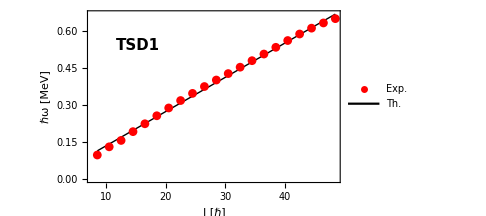

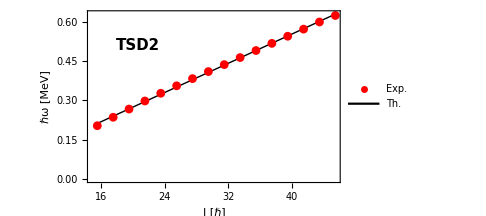

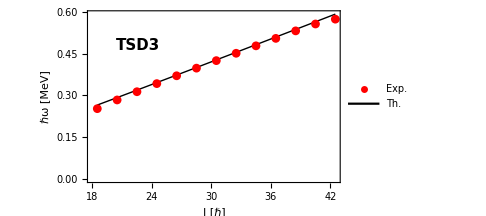

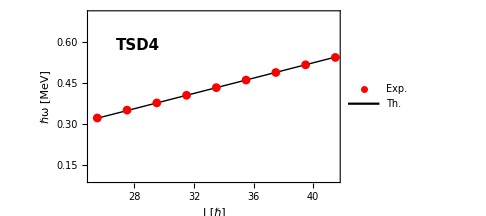

```mathematica
hrotPlot[exp_,data_,label_,range_]:=Show[ListPlot[{exp,data},LabelStyle->{18,Black,FontFamily->"Times"},PlotLegends->Placed[{"Exp.","Th."},{0.8,0.25}],Frame->True,Axes->False,Joined->{False,True},PlotStyle->{{Red,Thick},{Black,Thick}},PlotMarkers->{{"●", 9},None},AspectRatio->0.6,ImageSize->Medium,FrameStyle->Directive[Black],FrameLabel->{"I [ℏ]","ℏω [MeV]"},PlotRange->range],Epilog->Inset[Style[label,Italic,Bold,Black,15,FontFamily->"Arial"],Scaled[{0.2,0.8}]]];
h1=hrotPlot[hrot1Exp,hrot1Th,"TSD1",Full]
exporter[h1,prepath["tsd1"]];
h2=hrotPlot[hrot2Exp,hrot2Th,"TSD2",Full]
exporter[h2,prepath["tsd2"]];
h3=hrotPlot[hrot3Exp,hrot3Th,"TSD3",Full]
exporter[h3,prepath["tsd3"]];
h4=hrotPlot[hrot4Exp,hrot4Th,"TSD4",{0.1,0.7}]
exporter[h4,prepath["tsd4"]];
```